Euler Method:

```mathematica
ClearAll["Global`*"]
```

```mathematica
eulerGen[Func_,X0_,tf_,nMax_]:=Module[{h,dataset,prev,next,rate},
h=(tf-X0[[1]])/nMax//N;
For[dataset={X0},
Length[dataset]<=nMax,
AppendTo[dataset,next],
prev=Last[dataset];
rate=Through[Func@@prev];
next=prev+h rate;];
Return[dataset];]
```

```mathematica
id[t_,x_,v_]=1;
xdot[t_,x_,v_]=v;
vdot[t_,x_,v_]=-x+Cos[ω t];
```

```mathematica
initial={0,0,1};
```

```mathematica
ω=0.9;
```

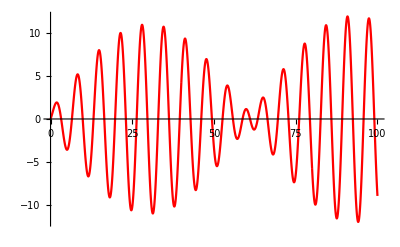

```mathematica
data=eulerGen[{id,xdot,vdot},initial,100,20000];
ListPlot[data[[;;,1;;2]],PlotMarkers->None,PlotRange->Full,PlotStyle->Red,Joined->True]
```

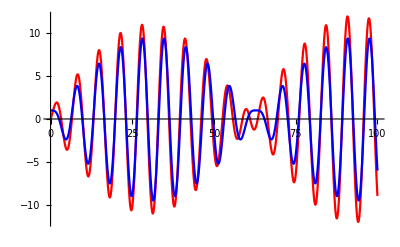

```mathematica
Show[ListPlot[data[[;;,1;;2]],Joined->True,PlotMarkers->None,PlotRange->Full,PlotStyle->Red],Plot[1/(1-ω^2)(-ω^2 Cos[t]+Cos[ω t]),{t,0,100},PlotRange->Full,PlotStyle->Blue]]
```

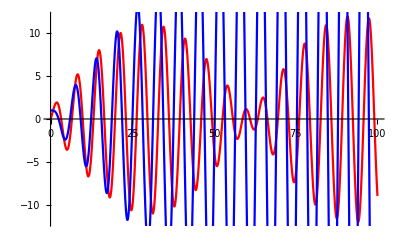

```mathematica
Show[ListPlot[data[[;;,1;;2]],Joined->True,PlotMarkers->None,PlotRange->Full,PlotStyle->Red],Plot[Cos[t]+t/2 Sin[t],{t,0,100},PlotStyle->Blue,PlotRange->Full]]
```

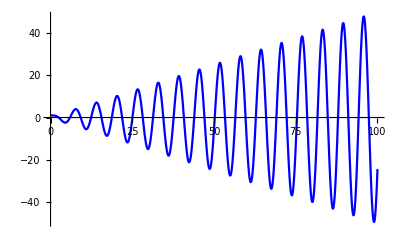

```mathematica
Plot[Cos[t]+t/2 Sin[t],{t,0,100},PlotStyle->Blue,PlotRange->Full]
```

Improved Euler Method:

```mathematica
Clear["Global`*"]
```

```mathematica
eulerImp[F_,X0_,tf_,nMax_]:=Module[{h,datas,next,prev,rate,rate1,next1},
h=(tf-X0[[1]])/nMax//N;
For[datas={X0},
Length[datas]<=nMax,
AppendTo[datas,next],
prev=Last[datas];
rate=Through[F@@prev];
next1=prev+h rate;
rate1=Through[F@@next1];
next=prev+h/2( rate1+rate);];
Return[datas];]
```

```mathematica
ω=0.9;
id[t_,x_,v_]=1;
xdot[t_,x_,v_]=v;
vdot[t_,x_,v_]=-x+Cos[ω t];
initial={0,1,0};
```

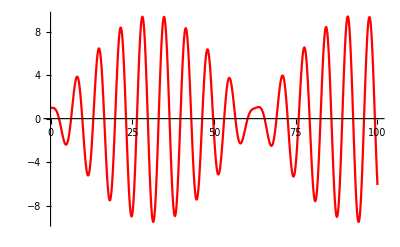

```mathematica
data=eulerImp[{id,xdot,vdot},initial,100,2000];
ListPlot[data[[;;,1;;2]],PlotMarkers->None,PlotRange->Full,PlotStyle->Red,Joined->True]
```

```mathematica
Clear[ω]
```

```mathematica
Limit[1/(1-ω^2)(-ω^2 Cos[t]+Cos[ω t]), ω -> 1]
```

Cos[t]+1/2 t Sin[t]

```mathematica
Clear[ω]
```

```mathematica
ω = 0.9;
```

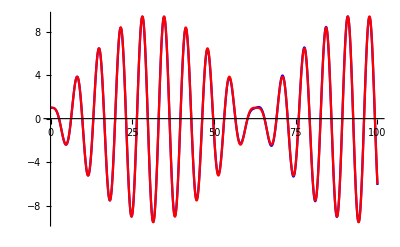

```mathematica
Show[ListPlot[data[[;;,1;;2]],Joined->True,PlotMarkers->None,PlotRange->Full,PlotStyle->Blue],Plot[1/(1-ω^2)(-ω^2 Cos[t]+Cos[ω t]),{t,0,100},PlotRange->Full,PlotStyle->Red]]
```

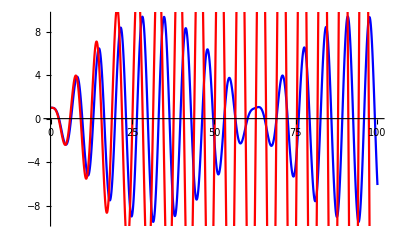

```mathematica
ω=1;
Show[ListPlot[data[[;;,1;;2]],Joined->True,PlotMarkers->None,PlotRange->Full,PlotStyle->Blue],Plot[(Cos[t]+t/2 Sin[t]),{t,0,100},PlotRange->Full,PlotStyle->Red]]
```

```mathematica
Clear["Global`*"]
```

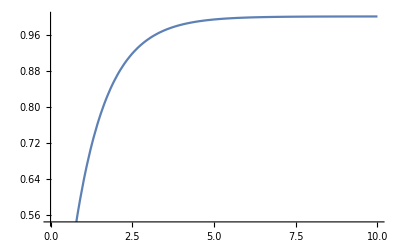

```mathematica
vfunc[t_]=1-ⅇ^-t;
Plot[vfunc[t],{t,0,10}]
```

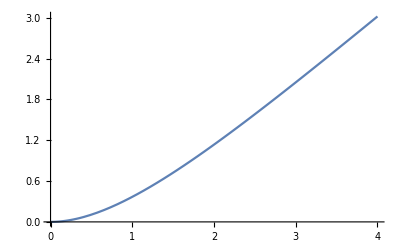

```mathematica
yFunc[t_]=t+ⅇ^-t-1;
Plot[yFunc[t],{t,0,4}]
```

```mathematica
Clear["Global`*"]
```

```mathematica
rk4[F_,X0_,tf_,nMax_]:=Module[{h,data1,prev,rate1,rate2,rate3,rate4,next},h=(tf-X0[[1]])/nMax//N;
For[data1={X0},
Length[data1]<=nMax,
AppendTo[data1,next],
prev=Last[data1];
rate1=F@prev;
rate2=F@(h/2 rate1+prev);
rate3=F@(h/2 rate2+prev);
rate4=F@(prev+h rate3);
next=prev+(h/6(rate1+2 rate2+2rate3+rate4));
];Return[data1];]
```

```mathematica
ratefunc[{t_,x_,v_}]={1,v,1-v};
initialv={0,0,0};
```

```mathematica
yodata=rk4[ratefunc,initialv,4,300];
```

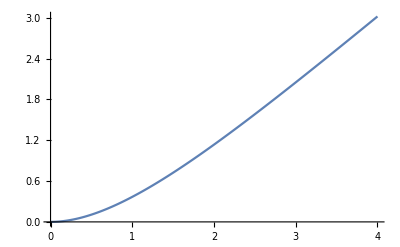

```mathematica
ListPlot[yodata[[;;,1;;2]],Joined->True,PlotRange->Full,PlotMarkers->None]
```

```mathematica
solx[t_]=t+ⅇ^-t-1;
```

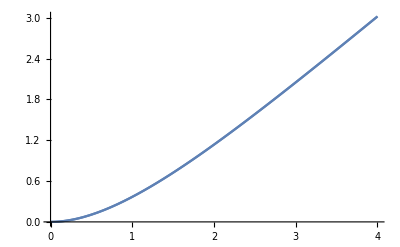

```mathematica
Show[ListPlot[yodata[[;;,1;;2]],Joined->True,PlotRange->Full,PlotMarkers->None],Plot[solx[t],{t,0,4},PlotRange->Full],PlotMarkers->None]
```

Escape Velocity:

```mathematica
Clear["Global`*"]
Manipulate[Plot[√(v^2-2+2/x),{x,0,100},PlotLabel->v],{v,0 ,10}]
```

```mathematica
rk4[F_,X0_,tf_,nMax_]:=Module[{h,data1,prev,rate1,rate2,rate3,rate4,next},h=(tf-X0[[1]])/nMax//N;
For[data1={X0},
Length[data1]<=nMax,
AppendTo[data1,next],
prev=Last[data1];
rate1=F@prev;
rate2=F@(h/2 rate1+prev);
rate3=F@(h/2 rate2+prev);
rate4=F@(prev+h rate3);
next=prev+(h/6(rate1+2 rate2+2rate3+rate4));
];Return[data1];]
```

```mathematica
esFunc[{t_,x_,v_}]={1,v,-1/x^2};
initial={0,1,√2};
soles[t_]=(3/2 √2 t+1)^(2.0/3.0);
```

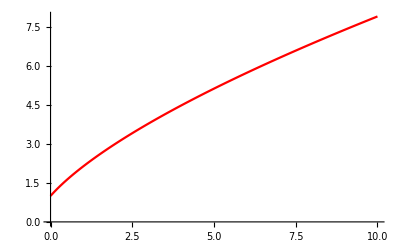

```mathematica
esdata=rk4[esFunc,initial,10,100];
ListPlot[esdata[[;;,1;;2]],Joined->True,PlotRange->Full,PlotStyle->Red]
```

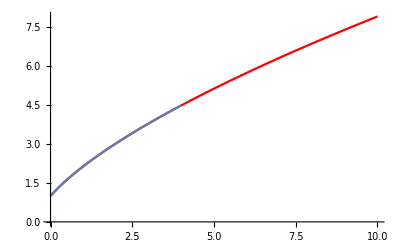

```mathematica
Show[ListPlot[esdata[[;;,1;;2]],Joined->True,PlotRange->Full,PlotStyle->Red],Plot[soles[t],{t,0,4},PlotRange->Full]]
```

```mathematica
Clear["Global`*"]
```

```mathematica
({{t}, {x}, {v}})=({{1}, {v}, {-1/x^2-ⅇ^(-(x-1))}})
```

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of -ⅇ^(1-x).

Hold[{{1},{v},{-ⅇ^(1-x)-1/x^2}}]

```mathematica
Clear["Global`*"]
```

```mathematica
rk4[F_,Xθ_,tf_,nmax_]:=Module[{h,data1,prev,rate1,rate2,rate3,rate4,next},h=(tf-Xθ[[1]])/nmax//N;
For[data1={Xθ},Length[data1]<=nmax,AppendTo[data1,next],prev=Last[data1];
rate1=F@prev;
rate2=F@(prev+h/2 rate1);
rate3=F@(prev+h/2 rate2);
rate4=F@(prev+h rate3);
next=prev+h/6 (rate1+2 rate2+2 rate3+rate4);];
Return[data1];]

ratefunc[{t_,x_,v_}]={1,v,-1/x^2 - ⅇ^(-(x-1))v};
initial={0,1,0.1};
```

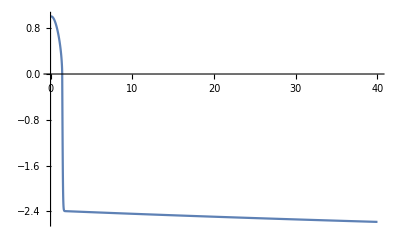

```mathematica
airdata=rk4[ratefunc,initial,40,3000];
ListPlot[airdata[[;;,1;;2]],Joined->True,PlotMarkers->None,PlotRange->Full]
```

Week 6 Lecture 5 Driven oscillator variations

```mathematica
Clear["Global`*"]
```

```mathematica
rk4[F_,Xθ_,tf_,nmax_]:=Module[{h,datalist,prev,rate1,rate2,rate3,rate4,next},h=(tf-Xθ[[1]])/nmax//N;
For[datalist={Xθ},Length[datalist]<=nmax,AppendTo[datalist,next],prev=Last[datalist];
rate1=F@prev;
rate2=F@(prev+h/2 rate1);
rate3=F@(prev+h/2 rate2);
rate4=F@(prev+h rate3);
next=prev+h/6(rate1+2 rate2+2 rate3+rate4);];
Return[datalist];]
```

```mathematica
DSolve[{x''[t] == -x[t] + 1, x[0] ==0, x'[0]== 0}, x[t], t]
```

{{x[t]→1-Cos[t]}}

```mathematica
ratefunc[{t_,x_,v_}]={1,v,1-x};
 drivsol[t_]=1-Cos[t];
drivinitial={0,0,0};
```

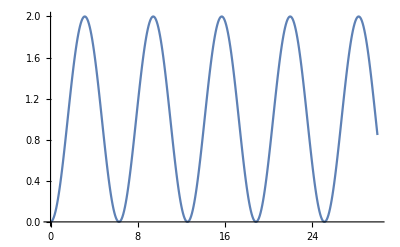

```mathematica
datap = rk4[ratefunc,drivinitial,30,400];
ListPlot[datap[[;;,1;;2]],Joined->True,PlotRange->Full,PlotMarkers->None]
```